### Set-Up

```mathematica
Sum[rho^k,{k,1,16}]-(1-rho^17)/(1-rho)
```

rho+rho^2+rho^3+rho^4+rho^5+rho^6+rho^7+rho^8+rho^9+rho^10+rho^11+rho^12+rho^13+rho^14+rho^15+rho^16-(1-rho^17)/(1-rho)

```mathematica
Simplify[rho+rho^2+rho^3+rho^4+rho^5+rho^6+rho^7+rho^8+rho^9+rho^10+rho^11+rho^12+rho^13+rho^14+rho^15+rho^16-rho (1-rho^16)/(1-rho)]
```

0

```mathematica
Mod[RandomVariate[GeometricDistribution[1/20],40],16]
```

{7,7,3,9,6,11,2,5,11,9,12,9,2,15,2,14,0,2,0,3,10,11,15,9,8,0,8,5,6,7,1,8,12,9,14,7,11,12,9,8}

```mathematica
RandomVariate[GeometricDistribution[1/400],40]
```

{189,448,235,555,33,16,132,128,93,455,7,192,12,164,400,150,1083,15,175,1826,230,664,172,66,931,492,68,543,55,998,1844,559,323,153,96,321,168,1418,47,663}

```mathematica
XX=Mod[RandomVariate[GeometricDistribution[1/10],4^3],3]+1
```

{1,3,3,2,1,1,1,2,2,2,1,1,3,3,2,3,3,3,1,2,3,3,1,1,1,2,2,2,1,3,3,3,3,1,1,3,1,1,1,1,2,1,1,2,3,1,3,3,1,1,2,2,1,2,1,2,2,3,1,3,3,2,1,2}

```mathematica
XX={11,4,0,13,12,2,2,10,1,13,6,6,3,12,7,1,1,3,0,3,1,6,12,4,2,3,10,10,9,7,1,2,3,0,12,3,7,9,5,0,10,11,2,11,4,2,3,2,5,2,10,0,0,3,5,11,11,6,0,14,4,1,2,2}
```

{11,4,0,13,12,2,2,10,1,13,6,6,3,12,7,1,1,3,0,3,1,6,12,4,2,3,10,10,9,7,1,2,3,0,12,3,7,9,5,0,10,11,2,11,4,2,3,2,5,2,10,0,0,3,5,11,11,6,0,14,4,1,2,2}

```mathematica
RandomVariate[BinomialDistribution[1,1/2]]
```

1

```mathematica
Table[  RandomVariate[BinomialDistribution[1,1/2]]+
XX[[i]] ,{i,1,4^3},{j,1,4^3}]
```

```mathematica
TT1=Table[Table[If[k>=4^m,IntegerDigits[k,4][[m]],0],{m,1,3}],{k,0,63}]
```

{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{2,0,0},{2,0,0},{2,0,0},{2,0,0},{3,0,0},{3,0,0},{3,0,0},{3,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,1,0},{1,1,0},{1,1,0},{1,1,0},{1,2,0},{1,2,0},{1,2,0},{1,2,0},{1,3,0},{1,3,0},{1,3,0},{1,3,0},{2,0,0},{2,0,0},{2,0,0},{2,0,0},{2,1,0},{2,1,0},{2,1,0},{2,1,0},{2,2,0},{2,2,0},{2,2,0},{2,2,0},{2,3,0},{2,3,0},{2,3,0},{2,3,0},{3,0,0},{3,0,0},{3,0,0},{3,0,0},{3,1,0},{3,1,0},{3,1,0},{3,1,0},{3,2,0},{3,2,0},{3,2,0},{3,2,0},{3,3,0},{3,3,0},{3,3,0},{3,3,0}}

```mathematica
TT2=Table[Table[If[TT1[[i]][[m]]== TT1[[j]][[m]],1,0],{m,1,3}], {i,1,64},{j,1,64}];
```

```mathematica
TT3=Table[Table[ Product[TT2[[i,j,m']],{m',m,3}],{m,1,3}], {i,1,64},{j,1,64}];
```

```mathematica
Dimensions[TT3]
```

{64,64,3}

```mathematica
TT3[[4]]
```

{{1,1,1},{1,1,1},{1,1,1},{1,1,1},{0,1,1},{0,1,1},{0,1,1},{0,1,1},{0,1,1},{0,1,1},{0,1,1},{0,1,1},{0,1,1},{0,1,1},{0,1,1},{0,1,1},{0,1,1},{0,1,1},{0,1,1},{0,1,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,1,1},{0,1,1},{0,1,1},{0,1,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,1,1},{0,1,1},{0,1,1},{0,1,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1}}

```mathematica
Flatten[{0,TT3[[4,2]]}]
```

{0,1,1,1}

```mathematica
TT4=Table[Flatten[{If[j==i+1,1,If[j==i-1,1,0]],TT3[[i,j]]}], {i,1,64},{j,1,64}];
```

```mathematica
TT4[[4]]
```

{{0,1,1,1},{0,1,1,1},{1,1,1,1},{0,1,1,1},{1,0,1,1},{0,0,1,1},{0,0,1,1},{0,0,1,1},{0,0,1,1},{0,0,1,1},{0,0,1,1},{0,0,1,1},{0,0,1,1},{0,0,1,1},{0,0,1,1},{0,0,1,1},{0,0,1,1},{0,0,1,1},{0,0,1,1},{0,0,1,1},{0,0,0,1},{0,0,0,1},{0,0,0,1},{0,0,0,1},{0,0,0,1},{0,0,0,1},{0,0,0,1},{0,0,0,1},{0,0,0,1},{0,0,0,1},{0,0,0,1},{0,0,0,1},{0,0,1,1},{0,0,1,1},{0,0,1,1},{0,0,1,1},{0,0,0,1},{0,0,0,1},{0,0,0,1},{0,0,0,1},{0,0,0,1},{0,0,0,1},{0,0,0,1},{0,0,0,1},{0,0,0,1},{0,0,0,1},{0,0,0,1},{0,0,0,1},{0,0,1,1},{0,0,1,1},{0,0,1,1},{0,0,1,1},{0,0,0,1},{0,0,0,1},{0,0,0,1},{0,0,0,1},{0,0,0,1},{0,0,0,1},{0,0,0,1},{0,0,0,1},{0,0,0,1},{0,0,0,1},{0,0,0,1},{0,0,0,1}}

```mathematica
TT5=Table[ Sum[If[XX[[i]]≥m,If[XX[[j]]≥m,
TT3[[i,j,m]] 1/2 (1/4)^(m-1),0],0],{m,1,4}]
, {i,1,64},{j,1,64}];
```

```mathematica
TT5[[4]]
```

{1/2,5/8,5/8,5/8,0,0,0,1/8,1/8,1/8,0,0,1/8,1/8,1/8,1/8,1/8,1/8,0,1/8,0,0,0,0,0,0,0,0,0,0,0,0,1/8,0,0,1/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/8,1/8,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
RandomVariate[BinomialDistribution[1,1/400],4]
```

{0,0,0,0}

```mathematica
TT6=Table[RandomVariate[BinomialDistribution[1,TT5[[i,j]]],1]
, {i,1,64},{j,1,64}];
```

```mathematica
Total[TT6]
```

{{3},{3},{8},{4},{5},{4},{6},{6},{8},{10},{4},{5},{6},{8},{6},{11},{6},{4},{4},{5},{3},{4},{1},{2},{0},{3},{2},{5},{2},{2},{3},{4},{4},{6},{3},{6},{2},{1},{1},{3},{2},{2},{1},{3},{3},{2},{2},{2},{5},{4},{7},{6},{1},{2},{1},{5},{0},{3},{2},{5},{4},{0},{4},{5}}

```mathematica
UU0=Table[0,{i,1,64}]
```

```mathematica
UU0={0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
```

{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
UU1=Flatten[UU0.TT6]
```

{0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
II0=UU0;
```

```mathematica
Total[II0]
```

1

```mathematica
II1=Table[If[II0[[i]]==0,If[UU1[[i]]>0,1,0],1],{i,1,64}]
```

{0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Total[II1]
```

5

```mathematica
UU2=Flatten[II1.TT6]
```

{0,0,2,0,3,3,3,3,1,1,0,0,0,0,0,0,3,2,3,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
II2=Table[If[II1[[i]]==0,If[UU2[[i]]>0,1,0],1],{i,1,64}]
```

{0,0,1,0,1,1,1,1,1,1,0,0,0,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Total[II2]
```

12

```mathematica
UU3=Flatten[II2.TT6]
```

{0,2,4,1,5,4,6,6,3,4,1,1,1,2,2,2,4,4,4,5,0,0,0,0,0,0,0,0,0,0,1,0,2,2,0,2,0,0,0,0,0,0,0,0,0,0,0,0,1,0,3,2,0,0,0,0,0,0,0,1,0,0,0,0}

```mathematica
II3=Table[If[II2[[i]]==0,If[UU3[[i]]>0,1,0],1],{i,1,64}]
```

{0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,0,0,0,0,0,0,1,0,0,0,0}

```mathematica
Total[II3]
```

27

```mathematica
UU4=Flatten[II3.TT6]
```

{2,3,5,4,5,4,6,6,7,10,4,4,4,6,6,9,6,4,4,5,0,0,0,0,0,0,0,0,0,1,2,1,4,6,2,6,0,0,0,0,0,0,0,0,0,0,0,0,5,3,6,6,0,0,0,0,0,2,0,2,0,0,0,0}

```mathematica
II4=Table[If[II3[[i]]==0,If[UU4[[i]]>0,1,0],1],{i,1,64}]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,0,0,0,0,0,1,0,1,0,0,0,0}

```mathematica
Total[II4]
```

33

```mathematica
UU4=Flatten[II3.TT6]
```

{2,3,5,4,5,4,6,6,7,10,4,4,4,6,6,9,6,4,4,5,0,0,0,0,0,0,0,0,0,1,2,1,4,6,2,6,0,0,0,0,0,0,0,0,0,0,0,0,5,3,6,6,0,0,0,0,0,2,0,2,0,0,0,0}

```mathematica
II4=Table[If[II3[[i]]==0,If[UU4[[i]]>0,1,0],1],{i,1,64}]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,0,0,0,0,0,1,0,1,0,0,0,0}

```mathematica
Total[II4]
```

33

```mathematica
UU5=Flatten[II4.TT6]
```

{3,3,7,4,5,4,6,6,8,10,4,5,5,6,6,10,6,4,4,5,0,0,0,0,0,0,0,1,2,2,2,1,4,6,3,6,0,0,0,0,0,0,0,0,0,0,1,0,5,4,7,6,0,0,0,0,0,2,1,3,0,0,0,2}

```mathematica
II5=Table[If[II4[[i]]==0,If[UU5[[i]]>0,1,0],1],{i,1,64}]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,1,0,1,1,1,1,0,0,0,0,0,1,1,1,0,0,0,1}

```mathematica
Total[II5]
```

38

```mathematica
UU6=Flatten[II5.TT6]
```

{3,3,7,4,5,4,6,6,8,10,4,5,5,6,6,10,6,4,4,5,0,0,0,0,0,0,0,2,2,2,3,3,4,6,3,6,0,0,0,0,0,0,0,1,1,0,1,1,5,4,7,6,0,0,0,0,0,2,2,4,1,0,1,3}

```mathematica
II6=Table[If[II5[[i]]==0,If[UU6[[i]]>0,1,0],1],{i,1,64}]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,1,1,0,1,1,1,1,1,1,0,0,0,0,0,1,1,1,1,0,1,1}

```mathematica
Total[II6]
```

43

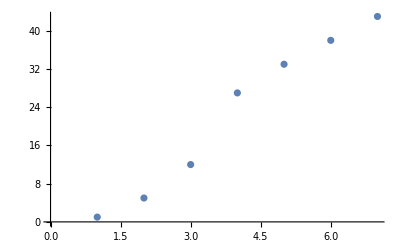

```mathematica
ListPlot[{1,5,12,27,33,38,43}]
```

### Cruise-ship

```mathematica
XX=Mod[RandomVariate[GeometricDistribution[1/10],4^6],7]
```

{2,1,4,1,0,2,2,6,6,1,1,5,2,3,5,0,5,3,1,4,1,2,2,3,2,3,1,0,1,6,1,2,3,2,5,0,1,0,2,0,0,0,3,3,2,1,4,2,1,4,1,4,5,0,6,3,0,0,6,3,3,0,2,1,3,4,0,4,0,4,5,2,1,4,6,0,0,1,1,0,6,5,1,2,5,1,0,2,0,3,0,0,1,5,2,6,0,3,3,4,5,4,6,3,5,3,3,2,2,1,4,2,6,2,2,4,2,2,5,1,4,4,0,1,0,4,2,2,1,0,1,1,1,0,0,1,4,6,5,1,1,0,1,1,3,2,4,0,2,5,2,3,3,0,0,3,0,4,2,2,4,4,1,1,5,0,1,2,0,1,3,5,3,6,4,4,5,0,3,6,2,3,1,4,2,4,0,2,2,3,0,4,6,0,4,6,3,3,4,4,2,6,5,2,3,4,0,3,5,4,2,5,2,0,1,0,4,3,6,5,5,4,5,2,5,4,3,3,0,0,3,0,1,0,5,3,4,6,3,5,5,4,3,5,0,4,1,2,3,0,3,1,0,2,1,2,1,2,6,3,3,5,1,4,1,5,6,5,6,2,5,2,2,6,3,3,4,0,2,2,2,5,4,2,3,6,6,5,1,3,3,2,2,0,3,2,3,2,3,4,3,3,1,5,1,3,3,0,5,4,6,5,5,5,2,4,3,3,1,0,0,0,4,2,3,0,0,6,5,0,4,2,4,5,1,2,1,0,4,6,3,2,0,0,0,3,4,6,2,4,0,1,5,2,5,0,3,0,5,4,2,5,1,0,5,1,1,0,0,5,4,6,0,2,1,4,3,2,6,0,4,0,4,0,0,2,0,5,1,5,2,5,3,4,3,0,6,1,1,6,6,6,1,6,3,2,3,3,1,5,1,0,3,5,4,0,6,6,4,3,5,1,4,3,5,4,6,5,6,0,0,6,3,2,5,3,6,4,0,1,5,0,1,4,6,5,1,0,6,4,0,3,2,1,5,3,1,2,5,6,0,4,5,2,1,0,5,5,5,2,0,3,2,3,5,1,0,3,6,1,6,3,2,1,6,5,2,5,2,5,3,1,6,1,3,5,6,0,1,5,6,4,4,4,3,2,6,6,4,4,3,0,2,3,1,0,0,5,4,0,0,2,5,2,2,0,6,5,4,6,3,0,4,0,0,0,0,4,3,4,0,4,3,0,2,0,2,0,5,3,5,5,4,2,5,2,3,0,2,6,4,1,4,2,2,4,1,1,0,5,2,3,6,3,4,4,5,2,3,4,1,0,6,2,0,6,6,1,1,6,4,3,0,0,6,0,2,5,2,5,2,1,6,5,6,1,0,3,1,5,0,0,3,6,0,5,0,1,2,6,1,0,5,2,5,0,1,4,0,0,1,5,1,0,3,0,3,5,0,2,6,0,1,2,1,0,5,3,0,4,2,1,1,0,4,4,5,0,3,3,3,5,3,6,4,1,3,0,3,0,2,3,1,1,0,5,5,5,1,0,6,2,6,5,2,1,3,4,0,4,1,4,5,0,5,1,4,4,3,5,6,1,0,5,6,1,5,1,1,0,6,3,4,3,4,4,0,3,5,0,4,5,0,0,4,0,2,0,5,0,1,0,2,0,0,3,3,3,0,1,2,6,4,4,4,3,2,0,2,4,6,1,5,1,1,2,4,2,5,1,4,2,2,2,2,3,0,2,3,0,0,4,0,1,6,2,3,5,2,1,0,4,4,2,4,5,1,6,0,1,6,2,1,4,0,0,4,3,0,4,5,5,6,4,0,4,1,3,1,3,0,6,5,0,5,5,1,3,4,1,0,4,5,3,6,3,0,2,2,6,5,1,2,6,2,0,4,4,0,4,3,1,2,5,1,0,3,0,1,1,3,5,5,6,4,5,0,0,4,1,3,5,2,4,1,2,5,3,0,2,3,6,4,2,6,5,1,2,1,1,2,4,0,5,1,2,2,1,5,0,4,4,0,3,0,3,5,2,1,2,4,1,6,0,0,0,1,3,4,5,5,6,4,0,4,0,2,6,1,4,5,2,1,2,0,2,5,0,2,1,6,1,0,4,1,2,2,5,2,2,5,1,6,4,0,4,0,2,6,1,3,0,4,0,4,2,4,2,3,0,3,2,0,2,0,5,2,4,1,1,0,0,4,6,1,3,2,1,0,3,0,0,2,1,0,4,6,6,3,2,2,1,2,5,4,1,4,4,0,4,6,0,4,2,3,3,6,1,1,1,6,3,2,1,4,0,0,1,5,3,3,0,0,1,1,1,5,1,1,5,4,5,2,3,1,0,4,1,4,3,2,3,0,2,0,2,2,1,0,4,1,3,6,5,6,0,0,1,6,6,3,3,6,2,6,2,6,0,0,2,6,3,3,2,2,5,4,1,1,1,3,4,5,3,3,3,4,0,2,3,3,5,4,2,5,4,1,6,0,5,0,3,1,2,1,0,1,1,3,6,2,5,0,0,0,2,0,6,3,5,2,2,5,5,0,4,1,6,3,4,1,3,0,1,0,3,1,5,0,1,6,0,1,1,4,4,5,5,6,0,2,1,4,2,4,5,3,6,4,5,3,2,6,3,2,0,2,6,2,4,5,3,4,3,1,5,2,0,3,4,6,0,2,1,4,0,2,1,2,3,0,1,0,3,1,3,1,0,1,2,3,4,3,5,1,5,0,2,2,5,0,1,0,1,5,6,3,2,0,1,1,0,3,3,2,1,0,0,5,0,6,0,1,5,3,1,0,4,1,6,1,3,1,6,0,2,1,1,1,5,0,0,1,2,4,0,4,2,0,6,5,5,1,6,2,3,2,1,4,6,6,0,0,0,4,4,0,2,0,6,1,2,2,0,5,5,3,2,3,1,5,4,1,2,1,6,4,5,1,6,5,2,5,3,3,0,2,6,0,0,2,0,2,0,0,1,5,3,2,1,5,2,5,2,0,5,0,5,0,1,5,1,3,5,2,5,0,5,4,6,3,4,4,1,5,2,3,0,1,6,1,2,3,2,3,4,1,1,3,2,2,0,4,2,4,0,0,4,5,0,0,3,1,5,1,1,2,5,1,1,4,3,1,2,0,6,2,2,1,6,6,0,3,3,2,6,1,3,4,4,0,0,3,5,6,0,1,1,6,6,1,2,5,4,3,3,1,4,4,1,3,4,0,6,3,2,1,5,3,3,6,2,5,1,1,0,5,0,2,4,1,2,4,4,0,2,4,0,5,6,3,0,3,4,2,4,1,1,1,4,1,0,2,2,0,6,2,2,0,4,0,4,0,2,4,2,2,2,2,0,3,1,1,2,3,6,6,6,4,4,6,3,0,2,1,4,0,5,2,1,1,5,5,2,1,2,3,0,5,4,3,4,2,2,2,2,0,1,0,1,2,1,3,3,5,5,6,5,4,0,2,2,4,4,1,6,0,3,1,0,6,4,5,0,0,1,3,2,6,3,6,6,6,5,6,2,4,4,4,2,1,6,1,5,3,5,1,0,1,3,5,2,0,5,4,3,4,4,4,3,5,2,6,3,2,0,6,0,4,6,4,4,4,4,6,6,3,1,5,5,0,4,6,1,2,0,4,0,4,2,0,6,0,3,1,1,0,4,0,2,0,1,0,4,6,0,1,1,2,0,5,2,2,1,5,0,0,6,0,3,1,4,2,3,0,2,4,2,2,5,4,5,5,4,3,4,0,3,3,3,0,2,0,3,6,2,6,4,0,4,4,3,2,2,5,5,4,5,5,1,3,6,0,5,2,1,5,5,0,4,1,4,3,2,1,0,0,0,4,3,0,5,3,0,0,6,2,4,6,1,2,1,0,2,3,2,6,0,1,1,4,6,1,3,3,1,5,1,2,3,1,3,0,5,1,0,3,2,6,0,0,4,1,1,3,2,1,3,6,4,2,4,3,5,5,1,4,4,6,6,0,6,0,1,2,1,5,2,1,4,0,2,0,3,3,3,5,3,2,5,5,6,4,2,6,3,5,1,5,3,3,6,0,5,0,0,1,1,4,1,3,0,0,0,2,6,5,1,1,3,4,5,4,5,0,6,5,4,1,5,1,4,4,3,2,4,0,0,3,0,3,4,5,1,1,5,0,1,0,5,5,2,5,5,0,0,2,3,5,2,2,2,5,1,0,0,0,3,0,2,3,0,5,1,1,1,0,4,4,0,1,5,3,3,0,6,3,4,1,1,5,5,4,4,0,6,3,3,1,4,2,1,2,0,3,0,0,0,6,5,1,2,0,6,5,0,1,1,3,1,1,5,0,2,3,1,5,0,0,1,5,0,5,2,2,0,1,2,3,2,4,1,0,2,4,5,5,1,3,3,0,6,0,4,3,6,5,3,4,3,3,1,0,5,0,5,4,0,6,3,0,1,1,2,5,0,0,3,0,1,4,1,0,6,5,4,1,5,4,0,6,3,3,1,5,0,5,5,2,5,0,4,6,0,1,0,0,3,1,5,0,5,1,2,2,5,5,5,5,4,2,5,3,1,3,4,5,0,0,4,2,5,3,6,1,2,4,5,2,2,0,5,3,2,5,1,0,3,3,4,0,5,5,3,0,0,3,3,1,5,4,0,4,3,2,3,0,0,6,5,6,5,1,1,1,3,3,0,0,4,6,4,2,0,4,1,6,0,3,0,0,5,3,3,4,2,4,5,4,4,2,3,0,0,1,0,3,2,1,5,0,6,2,5,1,3,4,1,6,0,1,3,5,0,0,2,1,3,6,4,0,0,1,6,3,0,5,0,5,0,3,2,5,1,3,0,4,2,0,0,4,2,2,0,3,0,1,5,4,4,1,0,5,5,3,2,3,6,1,2,0,4,3,4,6,2,4,2,4,0,4,1,4,1,1,0,2,1,3,0,3,2,2,4,1,4,3,3,6,5,0,1,6,5,6,5,2,4,0,0,1,0,6,5,0,3,3,6,3,1,3,3,2,6,1,4,2,1,1,1,6,4,1,2,5,0,2,0,6,1,3,4,3,5,1,4,0,1,1,6,5,5,1,2,6,2,4,0,3,6,6,6,0,5,3,2,2,0,1,3,5,0,2,0,4,3,2,0,3,5,5,0,3,0,3,4,0,1,2,6,2,6,1,1,0,5,3,5,0,4,1,3,0,6,0,2,2,6,1,3,4,5,0,2,0,3,1,5,3,0,2,0,6,4,0,6,3,3,1,4,2,0,1,0,5,1,0,0,6,2,3,6,6,6,0,2,4,1,2,1,6,5,4,6,2,1,2,1,5,1,0,6,0,5,2,4,0,0,3,0,2,6,4,6,1,5,0,1,1,3,5,1,5,0,1,4,4,4,2,1,3,3,1,1,0,2,2,0,0,3,0,2,2,5,3,5,1,5,1,4,3,4,4,2,2,4,1,5,5,4,1,2,3,0,6,4,2,0,2,4,6,5,6,4,0,2,5,4,1,4,5,1,4,2,5,3,0,1,3,5,1,1,2,0,2,5,0,0,3,5,0,3,4,2,1,2,3,6,5,1,0,6,6,4,1,4,6,2,0,0,1,1,6,5,5,5,5,0,4,1,1,0,0,4,0,2,0,6,2,0,6,0,2,2,3,3,5,0,4,0,2,0,4,6,6,1,4,5,1,0,0,5,0,4,2,6,0,1,1,2,1,6,2,4,2,0,5,6,0,0,5,4,5,5,0,3,3,6,3,2,0,3,1,1,0,2,0,2,0,2,1,0,2,4,1,0,4,6,0,2,2,0,4,0,6,1,0,3,0,5,4,0,6,1,3,6,3,2,1,5,0,1,6,2,2,0,0,0,0,3,3,0,3,2,1,1,1,1,2,3,2,1,0,4,3,2,6,1,3,1,4,2,1,0,3,2,2,1,5,0,2,1,2,5,4,1,3,4,3,0,6,5,5,1,1,3,1,4,0,3,1,2,3,3,0,4,4,2,3,1,2,3,1,3,5,1,3,5,0,1,2,5,6,0,4,5,3,3,4,4,2,6,6,6,0,0,2,4,4,4,1,3,1,3,3,6,0,4,1,4,1,1,0,2,0,4,5,2,4,1,3,5,4,3,6,1,2,6,0,2,6,5,0,2,2,3,0,2,0,4,3,0,1,4,5,6,5,3,4,5,1,2,6,0,6,2,0,2,0,1,5,0,2,3,3,2,0,5,1,4,4,0,0,5,0,1,6,4,5,6,0,4,3,0,1,6,2,3,1,6,2,5,5,1,3,5,4,3,1,1,0,4,2,5,2,5,6,3,0,1,5,3,5,3,6,2,2,2,4,0,6,3,2,2,6,2,6,5,3,0,0,6,1,5,5,3,3,4,4,3,2,1,3,6,4,1,1,1,0,0,5,2,4,4,6,3,2,2,1,2,4,2,5,5,4,4,2,5,0,1,6,2,0,0,4,4,1,1,2,0,3,2,3,1,0,0,2,1,1,2,4,1,0,4,0,4,5,6,3,5,4,3,1,0,1,3,6,1,1,1,5,3,0,1,6,0,1,5,4,6,4,2,1,1,0,1,0,0,2,2,6,3,4,5,5,6,0,0,4,2,4,3,4,0,3,2,0,2,0,1,6,0,6,0,5,0,1,1,6,3,0,5,3,0,2,5,0,6,1,4,1,1,5,1,5,2,0,0,1,3,2,3,6,2,5,4,0,5,2,4,0,1,4,4,0,3,6,6,4,1,0,0,1,5,0,2,2,1,3,5,0,0,2,1,4,0,1,6,5,3,1,2,3,1,5,2,2,3,2,0,1,2,0,3,3,4,1,4,3,0,2,3,0,5,1,2,1,4,5,3,5,2,2,1,2,3,1,4,1,6,4,4,0,6,3,2,6,3,2,5,1,0,1,2,3,2,3,4,1,2,0,1,2,0,4,6,0,3,5,4,0,2,0,1,4,3,2,0,3,1,2,1,0,2,3,4,4,1,0,1,6,0,6,4,2,2,6,2,3,0,0,4,1,6,1,4,2,4,6,0,6,0,3,3,4,2,0,1,1,1,4,0,3,4,1,0,2,1,4,0,5,3,3,2,0,0,3,5,1,0,2,2,1,1,1,1,5,6,4,6,3,0,5,2,4,6,4,0,2,3,1,6,6,3,1,0,0,0,6,1,0,0,2,3,0,6,0,1,0,6,1,2,4,3,3,0,0,2,5,1,0,4,0,2,0,2,0,0,2,2,4,4,0,3,0,0,3,5,6,0,0,2,4,1,0,3,2,3,5,2,4,2,6,2,4,1,6,6,0,2,2,1,6,6,1,0,0,1,4,1,3,2,6,3,1,4,3,6,2,2,4,2,2,2,6,2,6,5,0,0,5,2,6,2,3,4,0,5,4,0,5,1,1,1,3,1,6,6,4,5,3,5,4,5,3,1,1,6,3,0,0,5,4,1,0,0,3,6,4,4,3,1,3,3,0,3,5,0,0,4,4,1,2,1,0,0,4,5,0,0,1,0,5,1,3,1,1,3,1,0,1,6,2,1,1,4,2,4,0,5,1,0,2,3,0,5,0,1,6,5,4,4,0,0,2,1,3,6,4,2,3,3,4,5,4,0,3,3,1,1,0,6,3,1,3,1,4,0,3,5,2,0,3,4,2,0,3,3,5,3,0,1,2,6,3,1,3,1,1,0,0,4,1,6,5,0,0,6,3,4,0,4,2,4,0,5,3,3,0,6,2,0,6,4,3,2,2,6,6,3,5,1,0,3,1,2,6,0,3,2,4,2,2,0,4,5,1,0,0,4,4,6,6,5,4,3,0,2,2,1,1,4,5,0,2,3,4,0,0,5,5,1,0,4,1,6,2,1,4,2,1,0,2,2,0,3,0,0,4,4,3,1,1,0,4,2,6,0,1,2,4,1,0,5,1,2,4,2,5,5,0,1,4,1,0,5,3,5,1,3,4,3,2,2,5,2,0,1,2,1,0,5,4,0,0,0,2,6,4,5,2,1,6,1,0,0,2,1,5,0,1,1,3,4,4,5,1,6,3,0,3,5,3,0,1,3,3,0,2,5,6,3,4,3,4,6,1,2,4,6,4,0,0,1,1,1,3,0,0,3,2,6,1,2,1,3,0,1,3,3,2,4,6,6,2,3,1,2,4,1,6,4,0,4,1,2,6,0,2,4,0,3,1,1,1,3,3,4,1,3,0,2,5,5,1,1,4,1,2,3,2,5,0,6,6,4,6,6,1,5,2,4,4,5,1,0,0,1,5,3,1,5,1,6,0,0,3,4,2,2,3,6,2,1,5,4,6,0,5,3,0,2,0,0,3,2,2,2,4,4,6,4,0,0,1,2,2,4,0,3,6,0,0,0,6,0,1,2,6,2,5,6,2,1,1,3,4,4,4,3,0,1,2,0,1,0,5,3,5,4,1,2,0,2,6,1,0,3,0,4,0,6,0,6,1,1,1,2,5,1,3,0,0,6,3,0,1,1,3,1,5,6,6,1,6,6,1,3,4,5,6,2,5,6,3,0,2,6,4,0,2,3,4,3,1,0,6,4,2,4,0,2,1,6,0,2,3,2,2,3,1,0,6,6,6,2,5,1,4,3,6,0,0,6,3,5,4,4,1,4,4,2,2,4,3,6,2,0,1,1,3,4,0,2,0,6,4,6,4,2,2,4,3,0,5,5,5,4,2,0,4,1,2,2,1,3,3,5,5,2,1,0,1,6,1,3,3,3,4,2,0,4,4,5,4,3,3,2,5,6,5,2,1,3,3,2,1,3,0,2,5,1,0,1,1,1,0,0,2,5,2,2,3,3,0,0,5,0,0,3,0,3,0,4,4,0,5,0,1,4,2,6,2,2,0,2,2,1,2,6,5,0,3,5,0,2,0,2,5,6,4,2,6,0,4,1,2,4,6,3,4,0,1,1,2,3,1,6,6,0,5,3,4,1,1,4,6,4,2,6,1,3,2,2,0,1,6,4,3,3,1,5,0,5,6,6,0,1,0,2,1,3,6,0,6,0,0,3,4,3,5,5,5,4,1,5,6,1,4,3,0,4,1,5,1,2,4,2,1,5,5,2,2,4,3,2,3,2,3,0,2,2,2,2,4,6,3,2,6,3,1,4,4,4,0,1,5,0,0,1,5,3,5,3,2,1,6,1,4,2,6,5,2,1,0,0,1,6,0,4,4,0,1,6,6,0,6,3,0,1,0,2,1,1,3,4,1,4,3,1,6,2,3,2,6,3}

```mathematica
RandomVariate[BinomialDistribution[1,1/2]]
```

1

```mathematica
TT1=Table[Table[If[k>=4^m,IntegerDigits[k,4][[m]],0],{m,1,6}],{k,0,4^6-1}]
```

{{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{1,0,0,0,0,0},{1,0,0,0,0,0},{1,0,0,0,0,0},{1,0,0,0,0,0},{2,0,0,0,0,0},{2,0,0,0,0,0},{2,0,0,0,0,0},4075,{3,3,3,3,1,0},{3,3,3,3,1,0},{3,3,3,3,2,0},{3,3,3,3,2,0},{3,3,3,3,2,0},{3,3,3,3,2,0},{3,3,3,3,3,0},{3,3,3,3,3,0},{3,3,3,3,3,0},{3,3,3,3,3,0}}
 |  |  |  |

```mathematica
TT2=Table[Table[If[TT1[[i]][[m]]== TT1[[j]][[m]],1,0],{m,1,6}], {i,1,4^6},{j,1,4^6}];
```

```mathematica
TT3=Table[Table[ Product[TT2[[i,j,m']],{m',m,6}],{m,1,6}], {i,1,4^6},{j,1,4^6}];
```

```mathematica
Dimensions[TT3]
```

{4096,4096,6}

```mathematica
TT3[[4]]
```

{{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{0,1,1,1,1,1},{0,1,1,1,1,1},{0,1,1,1,1,1},{0,1,1,1,1,1},{0,1,1,1,1,1},{0,1,1,1,1,1},{0,1,1,1,1,1},4075,{0,0,0,0,0,1},{0,0,0,0,0,1},{0,0,0,0,0,1},{0,0,0,0,0,1},{0,0,0,0,0,1},{0,0,0,0,0,1},{0,0,0,0,0,1},{0,0,0,0,0,1},{0,0,0,0,0,1},{0,0,0,0,0,1}}
 |  |  |  |

```mathematica
TT4=Table[Flatten[{If[j==i+1,1,If[j==i-1,1,0]],TT3[[i,j]]}], {i,1,4^6},{j,1,4^6}];
```

```mathematica
TT4[[4]]
```

{{0,1,1,1,1,1,1},{0,1,1,1,1,1,1},{1,1,1,1,1,1,1},{0,1,1,1,1,1,1},{1,0,1,1,1,1,1},{0,0,1,1,1,1,1},{0,0,1,1,1,1,1},{0,0,1,1,1,1,1},{0,0,1,1,1,1,1},4078,{0,0,0,0,0,0,1},{0,0,0,0,0,0,1},{0,0,0,0,0,0,1},{0,0,0,0,0,0,1},{0,0,0,0,0,0,1},{0,0,0,0,0,0,1},{0,0,0,0,0,0,1},{0,0,0,0,0,0,1},{0,0,0,0,0,0,1}}
 |  |  |  |

```mathematica
TT5=Table[ Sum[If[XX[[i]]≥m,If[XX[[j]]≥m,
TT3[[i,j,m]] 1/2 (1/4)^(m-1),0],0],{m,1,7}]
, {i,1,4^6},{j,1,4^6}];
```

```mathematica
TT5[[4]]
```

{1/2,1/2,1/2,1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
TT6=Table[RandomVariate[BinomialDistribution[1,TT5[[i,j]]],1]
, {i,1,4^6},{j,1,4^6}];
```

```mathematica
Total[TT6]
```

{{9},{2},{8},{2},{0},{15},{11},{22},{15},{9},{8},{18},{13},{14},{20},{0},{20},{17},{6},{15},{4},{8},{10},{15},{8},{11},{6},{0},{6},{17},{4},{11},{11},{13},{17},4026,{6},{2},{2},{0},{0},{3},{11},{0},{3},{6},{0},{1},{5},{2},{0},{5},{2},{0},{2},{0},{5},{3},{1},{2},{5},{1},{3},{4},{2},{6},{4},{2},{4},{5},{4}}
 |  |  |  |

```mathematica
UU0=Table[0,{i,1,4^6}]
```

```mathematica
UU0={0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
```

```mathematica
UU1=Flatten[UU0.TT6];
```

```mathematica
II0=UU0;
```

```mathematica
Total[II0]
```

1

```mathematica
II1=Table[If[II0[[i]]==0,If[UU1[[i]]>0,1,0],1],{i,1,4^6}];
```

```mathematica
Total[II1]
```

12

```mathematica
UU2=Flatten[II1.TT6];
```

```mathematica
II2=Table[If[II1[[i]]==0,If[UU2[[i]]>0,1,0],1],{i,1,4^6}];
```

```mathematica
Total[II2]
```

56

```mathematica
UU3=Flatten[II2.TT6];
```

```mathematica
II3=Table[If[II2[[i]]==0,If[UU3[[i]]>0,1,0],1],{i,1,4^6}];
```

```mathematica
Total[II3]
```

270

```mathematica
UU4=Flatten[II3.TT6];
```

```mathematica
II4=Table[If[II3[[i]]==0,If[UU4[[i]]>0,1,0],1],{i,1,4^6}];
```

```mathematica
Total[II4]
```

719

```mathematica
UU5=Flatten[II4.TT6];
```

```mathematica
II5=Table[If[II4[[i]]==0,If[UU5[[i]]>0,1,0],1],{i,1,4^6}];
```

```mathematica
Total[II5]
```

1210

```mathematica
UU6=Flatten[II5.TT6];
```

```mathematica
II6=Table[If[II5[[i]]==0,If[UU6[[i]]>0,1,0],1],{i,1,4^6}];
```

```mathematica
Total[II6]
```

1505

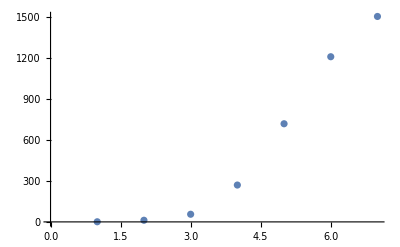

```mathematica
ListPlot[{1,12,56,270,719,1210,1505}]
```